```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20]
```

```mathematica
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20},16]
```

{imp8,imp10,imp3,imp7,imp19,imp5,imp12,imp9,imp16,imp20,imp4,imp11,imp17,imp18,imp14,imp2}

```mathematica
p[z_]:=ListLinePlot[Table[{x,y},{x,Range[1,100,1]},{y,Range[1,100,1]}][[z]],PlotStyle->Gray]
```

```mathematica
line[z_]:=ListLinePlot[Table[{x,z},{x,Range[1,100,0.1]}],PlotStyle->Gray]
```

```mathematica
line1[z_]:=ListLinePlot[Table[{x,z},{x,Range[0,100,0.1]}],PlotStyle->Blue]
```

```mathematica
p1[z_]:=ListLinePlot[Table[{z,y},{y,Range[0,21,1]}],PlotStyle->Blue]
```

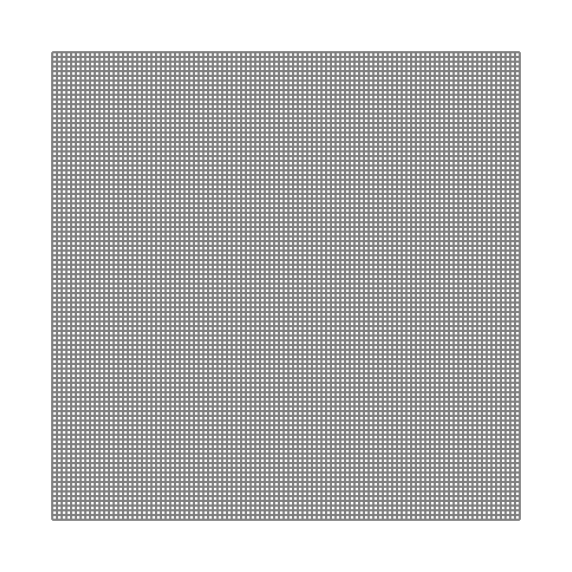

```mathematica
Show[Show[Table[p[z],{z,100}],Table[line[z],{z,100}],(*ListPlot[{{3,12},{11,17},{20,8},{8,5}},PlotStyle->Black],*)PlotRange->All],Axes->False,ImageSize->{560,560},AspectRatio->Full]
```

```mathematica
ab=Module[{list={RandomSample[{imp01,imp02,imp03,imp04,imp05,imp06,imp07,imp08,imp09,imp10,imp11,imp12,imp00,imp00,imp00,imp00,imp00,imp00,imp00,imp00}]}},
aa=Module[{},
Table[ToExpression[StringTake[StringCases[ToString[list],WordCharacter..][[x]],-2]],{x,20}]];
listn1=Transpose[Join[{Range[1,20,1]},{aa}]];listn2=Sort[Transpose[Join[{aa},{Range[1,20,1]}]]];
{listn1,listn2}]
```

{{{1,0},{2,3},{3,8},{4,0},{5,11},{6,0},{7,10},{8,0},{9,7},{10,4},{11,0},{12,2},{13,1},{14,0},{15,0},{16,12},{17,0},{18,9},{19,5},{20,6}},{{0,1},{0,4},{0,6},{0,8},{0,11},{0,14},{0,15},{0,17},{1,13},{2,12},{3,2},{4,10},{5,19},{6,20},{7,9},{8,3},{9,18},{10,7},{11,5},{12,16}}}

```mathematica
Clear[l30, l20, im1, im2, im3, im4, im5, im6, im7, im8, im9, im10, im11, im12, im13, im14, im15, im16, im17, 
  im19, im19, im20]
RandomSample[{im1, im2, im3, im4, im5, im6, im7, im8, im9, im10, im11, im12, im13, im14, im15, im16, im17, im19, 
   im19, im20}]
{im9, im15, im20, im2, im17, im16, im8, im14, im11, im12, im6, im4, im19, im7, im10, im1, im3, im13, im5, im19}
Flatten[Table[Position[aa, ToExpression[Table[StringJoin["im", ToString[x], ""], {x, 20}][[y]]]], {y, 20}]]
{19, 4, 13, 7, 5, 2, 10, 3, 15, 9, 18, 11, 16, 17, 6, 12}
Table[StringJoin["im", ToString[z], ""], 
  {z, Flatten[Table[Position[Flatten[Table[Position[aa, ToExpression[Table[StringJoin["im", ToString[x], ""], 
            {x, 20}][[y]]]], {y, 20}]], z], {z, 20}]]}]
{"im9", "im15", "im20", "im2", "im17", "im16", "im8", "im14", "im11", "im12", "im6", "im4", "im18", "im7", 
  "im10", "im1", "im3", "im13", "im5", "im19"}
ToExpression[Out[461]]
{im9, im15, im20, im2, im17, im16, im8, im14, im11, im12, im6, im4, im18, im7, im10, im1, im3, im13, im5, im19}
```

```mathematica
lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/20sq/lead_new/L_"<>ToString[ω]<>".dat"]],{ω,Range[0,4,0.01]}]
```

{1}
 |  |  |  |

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0,20]]},{ω,Range[0,4,0.01]}]
```

{{0.,20.},{0.01,20.},{0.02,19.9995},{0.03,19.},{0.04,19.},{0.05,19.},{0.06,19.},{0.07,19.},{0.08,19.},{0.09,18.0019},{0.1,18.},{0.11,18.},{0.12,18.},{0.13,18.},{0.14,18.},{0.15,18.},{0.16,18.},{0.17,18.},{0.18,18.},{0.19,18.},{0.2,17.0007},{0.21,17.},{0.22,17.},{0.23,17.},{0.24,17.},{0.25,17.},{0.26,17.},{0.27,17.},{0.28,17.},{0.29,17.},{0.3,17.},{0.31,17.},{0.32,17.},{0.33,17.},{0.34,17.},{0.35,16.0004},{0.36,16.},{0.37,16.},{0.38,16.},{0.39,16.},{0.4,16.},{0.41,16.},{0.42,16.},{0.43,16.},{0.44,16.},{0.45,16.},{0.46,16.},{0.47,16.},{0.48,16.},{0.49,16.},{0.5,16.},{0.51,16.},{0.52,16.},{0.53,15.9998},{0.54,15.0001},{0.55,15.},{0.56,15.},{0.57,15.},{0.58,15.},{0.59,15.},{0.6,15.},{0.61,15.},{0.62,15.},{0.63,15.},{0.64,15.},{0.65,15.},{0.66,15.},{0.67,15.},{0.68,15.},{0.69,15.},{0.7,15.},{0.71,15.},{0.72,15.},{0.73,15.},{0.74,15.},{0.75,14.9997},{0.76,14.0001},{0.77,14.},{0.78,14.},{0.79,14.},{0.8,14.},{0.81,14.},{0.82,14.},{0.83,14.},{0.84,14.},{0.85,14.},{0.86,14.},{0.87,14.},{0.88,14.},{0.89,14.},{0.9,14.},{0.91,14.},{0.92,14.},{0.93,14.},{0.94,14.},{0.95,14.},{0.96,14.},{0.97,14.},{0.98,14.},{0.99,14.},{1.,13.5},{1.01,13.},{1.02,13.},{1.03,13.},{1.04,13.},{1.05,13.},{1.06,13.},{1.07,13.},{1.08,13.},{1.09,13.},{1.1,13.},{1.11,13.},{1.12,13.},{1.13,13.},{1.14,13.},{1.15,13.},{1.16,13.},{1.17,13.},{1.18,13.},{1.19,13.},{1.2,13.},{1.21,13.},{1.22,13.},{1.23,13.},{1.24,13.},{1.25,13.},{1.26,13.},{1.27,12.0053},{1.28,12.},{1.29,12.},{1.3,12.},{1.31,12.},{1.32,12.},{1.33,12.},{1.34,12.},{1.35,12.},{1.36,12.},{1.37,12.},{1.38,12.},{1.39,12.},{1.4,12.},{1.41,12.},{1.42,12.},{1.43,12.},{1.44,12.},{1.45,12.},{1.46,12.},{1.47,12.},{1.48,12.},{1.49,12.},{1.5,12.},{1.51,12.},{1.52,12.},{1.53,12.},{1.54,12.},{1.55,11.9999},{1.56,11.0001},{1.57,11.},{1.58,11.},{1.59,11.},{1.6,11.},{1.61,11.},{1.62,11.},{1.63,11.},{1.64,11.},{1.65,11.},{1.66,11.},{1.67,11.},{1.68,11.},{1.69,11.},{1.7,11.},{1.71,11.},{1.72,11.},{1.73,11.},{1.74,11.},{1.75,11.},{1.76,11.},{1.77,11.},{1.78,11.},{1.79,11.},{1.8,11.},{1.81,11.},{1.82,11.},{1.83,11.},{1.84,11.},{1.85,10.9916},{1.86,10.},{1.87,10.},{1.88,10.},{1.89,10.},{1.9,10.},{1.91,10.},{1.92,10.},{1.93,10.},{1.94,10.},{1.95,10.},{1.96,10.},{1.97,10.},{1.98,10.},{1.99,10.},{2.,10.},{2.01,10.},{2.02,10.},{2.03,10.},{2.04,10.},{2.05,10.},{2.06,10.},{2.07,10.},{2.08,10.},{2.09,10.},{2.1,10.},{2.11,10.},{2.12,10.},{2.13,9.99999},{2.14,9.99997},{2.15,9.00836},{2.16,9.00002},{2.17,9.00001},{2.18,9.},{2.19,9.},{2.2,9.},{2.21,9.},{2.22,9.},{2.23,9.},{2.24,9.},{2.25,9.},{2.26,9.},{2.27,9.},{2.28,9.},{2.29,9.},{2.3,9.},{2.31,9.},{2.32,9.},{2.33,9.},{2.34,9.},{2.35,9.},{2.36,9.},{2.37,9.},{2.38,9.},{2.39,9.},{2.4,9.},{2.41,9.},{2.42,9.},{2.43,8.99999},{2.44,8.9999},{2.45,8.0001},{2.46,8.00001},{2.47,8.},{2.48,8.},{2.49,8.},{2.5,8.},{2.51,8.},{2.52,8.},{2.53,8.},{2.54,8.},{2.55,8.},{2.56,8.},{2.57,8.},{2.58,8.},{2.59,8.},{2.6,8.},{2.61,8.},{2.62,8.},{2.63,8.},{2.64,8.},{2.65,8.},{2.66,8.},{2.67,8.},{2.68,8.},{2.69,8.},{2.7,8.},{2.71,7.99999},{2.72,7.99998},{2.73,7.99471},{2.74,7.00003},{2.75,7.00001},{2.76,7.},{2.77,7.},{2.78,7.},{2.79,7.},{2.8,7.},{2.81,7.},{2.82,7.},{2.83,7.},{2.84,7.},{2.85,7.},{2.86,7.},{2.87,7.},{2.88,7.},{2.89,7.},{2.9,7.},{2.91,7.},{2.92,7.},{2.93,7.},{2.94,7.},{2.95,7.},{2.96,7.},{2.97,7.},{2.98,6.99999},{2.99,6.99997},{3.,6.49999},{3.01,6.00002},{3.02,6.00001},{3.03,6.},{3.04,6.},{3.05,6.},{3.06,6.},{3.07,6.},{3.08,6.},{3.09,6.},{3.1,6.},{3.11,6.},{3.12,6.},{3.13,6.},{3.14,6.},{3.15,6.},{3.16,6.},{3.17,6.},{3.18,6.},{3.19,6.},{3.2,6.},{3.21,6.},{3.22,6.},{3.23,5.99999},{3.24,5.99995},{3.25,5.00027},{3.26,5.00001},{3.27,5.},{3.28,5.},{3.29,5.},{3.3,5.},{3.31,5.},{3.32,5.},{3.33,5.},{3.34,5.},{3.35,5.},{3.36,5.},{3.37,5.},{3.38,5.},{3.39,5.},{3.4,5.},{3.41,5.},{3.42,5.},{3.43,5.},{3.44,5.},{3.45,4.99999},{3.46,4.99993},{3.47,4.00016},{3.48,4.00001},{3.49,4.},{3.5,4.},{3.51,4.},{3.52,4.},{3.53,4.},{3.54,4.},{3.55,4.},{3.56,4.},{3.57,4.},{3.58,4.},{3.59,4.},{3.6,4.},{3.61,4.},{3.62,4.},{3.63,3.99999},{3.64,3.99998},{3.65,3.99959},{3.66,3.00004},{3.67,3.00001},{3.68,3.},{3.69,3.},{3.7,3.},{3.71,3.},{3.72,3.},{3.73,3.},{3.74,3.},{3.75,3.},{3.76,3.},{3.77,3.},{3.78,2.99999},{3.79,2.99998},{3.8,2.99933},{3.81,2.00004},{3.82,2.00001},{3.83,2.},{3.84,2.},{3.85,2.},{3.86,2.},{3.87,2.},{3.88,2.},{3.89,1.99999},{3.9,1.99998},{3.91,1.9981},{3.92,1.00003},{3.93,1.00001},{3.94,1.},{3.95,0.999998},{3.96,0.999993},{3.97,0.999958},{3.98,0.000456674},{3.99,0.0000168049},{4.,5.34708×10^-6}}

```mathematica
Clear[imp,imp9,imp15,imp20,imp2,imp17,imp16,imp8,imp14,imp11,imp12,imp6,imp4,imp18,imp7,imp10,imp1,imp3,imp13,imp5,imp19]
aa=RandomSample[{imp13,imp1,imp18,imp16,imp17,imp10,imp11,imp14,imp12,imp8,imp15,imp19,imp2,imp9,imp7,imp5,imp6,imp3,imp20,imp4}]
bb:=Flatten[Table[Position[Flatten[Table[Position[aa,ToExpression[Table["imp"<>ToString[x]<>"",{x,20}][[y]]]],{y,20}]],z],{z,20}]]
cc:=Flatten[Table[Position[bb,x],{x,Range[1,20,1]}]]
dd=ToExpression[Table["imp"<>ToString[z]<>"",{z,cc}]]
leftright= Transpose[Join[{Range[1,20,1]},{bb}]]
downup= Transpose[Join[{cc},{Range[1,20,1]}]]
```

{imp6,imp20,imp9,imp15,imp18,imp12,imp13,imp17,imp2,imp11,imp3,imp10,imp7,imp14,imp19,imp5,imp16,imp1,imp4,imp8}

{imp18,imp9,imp11,imp19,imp16,imp1,imp13,imp20,imp3,imp12,imp10,imp6,imp7,imp14,imp4,imp17,imp8,imp5,imp15,imp2}

{{1,6},{2,20},{3,9},{4,15},{5,18},{6,12},{7,13},{8,17},{9,2},{10,11},{11,3},{12,10},{13,7},{14,14},{15,19},{16,5},{17,16},{18,1},{19,4},{20,8}}

{{18,1},{9,2},{11,3},{19,4},{16,5},{1,6},{13,7},{20,8},{3,9},{12,10},{10,11},{6,12},{7,13},{14,14},{4,15},{17,16},{8,17},{5,18},{15,19},{2,20}}

```mathematica
Clear[aa,bb,cc,dd]
```

```mathematica
Clear[aa,bb,cc,dd]
```

```mathematica
testhori[ϵ1_,ϵ_,m_,y_,x_,q_]:=Module[{Tin=T[1,m],T1=T[1,m],list1,list2,tra,
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{15,15}}->ω+ⅈ*0.0001-ϵ1]]],
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{16,16}}->ω+ⅈ*0.0001-ϵ1]]],
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{17,17}}->ω+ⅈ*0.0001-ϵ1]]],
imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{18,18}}->ω+ⅈ*0.0001-ϵ1]]],
imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{19,19}}->ω+ⅈ*0.0001-ϵ1]]],
imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{20,20}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]],aa,bb,cc,dd,leftright,downup},
tra[start_,stop_]:=Module[{},
aa={RandomSample[{imp13,imp1,imp18,imp16,imp17,imp10,imp11,imp14,imp12,imp8,imp15,imp19,imp2,imp9,imp7,imp5,imp6,imp3,imp20,imp4}]};
bb:=Flatten[Table[Position[Flatten[Table[Position[aa,ToExpression[Table["imp"<>ToString[ξ]<>"",{ξ,20}][[ψ]]]],{ψ,20}]],ζ],{ζ,20}]];
cc:=Flatten[Table[Position[bb,ξ],{ξ,Range[1,20,1]}]];
	dd={ToExpression[Table["imp"<>ToString[ζ]<>"",{ζ,cc}]]};
	leftright= Transpose[Join[{Range[1,20,1]},{bb}]];
downup= Transpose[Join[{cc},{Range[1,20,1]}]];
list1=aa;
list2=dd;
b1=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0,m]},     Do[J=Inverse[IdentityMatrix[m]-list1[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list1[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2=Module[{},sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list2[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list2[[1,ζ]],{ζ,start,stop}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
{b1,b2}];
m1=Table[{ω,tra[1,5][[q]]},{ω,Range[0,4,0.01]}];
m2=Table[{ω,tra[6,10][[q]]},{ω,Range[0,4,0.01]}];
m3=Table[{ω,tra[11,15][[q]]},{ω,Range[0,4,0.01]}];
m4=Table[{ω,tra[16,20][[q]]},{ω,Range[0,4,0.01]}];
υ1=Module[{},
ρ2:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m1[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ2=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m2[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ3=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m3[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];
υ4=Module[{},
ρ2:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/1imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/2imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/3imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/4imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/5imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/6imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[[1;;388]][[;;,1]],(m4[[1;;388,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/20sq/7imp_sudo_Q.dat"][[1;;388,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}];{υ1,υ2,υ3,υ4}]
```

```mathematica
hori=testhori[0.5,0,20,0,3.8]
verti=testverti[0.5,0,20,0,3.8]
Table[Position[hori[[x]],Min[hori[[x]]]],{x,4}]
Table[Position[verti[[x]],Min[verti[[x]]]],{x,4}]
```

{{0.0156647,0.011289,0.00937276,0.00834935,0.00802186,0.00945891,0.0116958},{0.0268604,0.0213742,0.0173826,0.0132655,0.010337,0.0113493,0.0130656},{0.0169529,0.0128086,0.00940194,0.00729474,0.00722863,0.0100194,0.0111887},{0.0238255,0.0165771,0.0109831,0.00930835,0.0102609,0.0136072,0.0159987}}

{{0.0194796,0.0151999,0.011874,0.00949141,0.00864123,0.0109263,0.0124646},{0.0189785,0.0127351,0.00734548,0.00479585,0.00541107,0.00917347,0.0125956},{0.0289683,0.0214367,0.0150791,0.0104471,0.00807328,0.00922831,0.0103698},{0.0337144,0.0262231,0.0195926,0.0146689,0.0125662,0.0137545,0.0159513}}

{{{5}},{{5}},{{5}},{{4}}}

{{{5}},{{4}},{{5}},{{5}}}

```mathematica
hori=testhori[0.5,0,20,0,3.8,1]
```

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,3,5,7,9,11,13,15,17,19,21,23,24,25,27,29,31,33,35,37,39,12,38,10,22,16,14,20,32,34,26,28,36,6,4,40,8,18,2,30}} cannot be transposed.

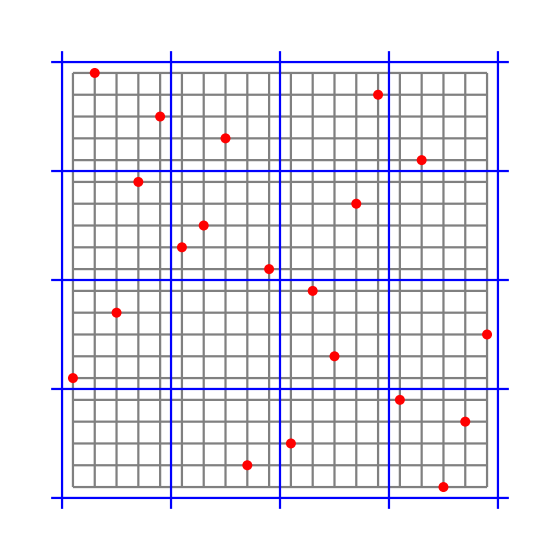

```mathematica
Show[Show[Table[p[z],{z,20}],Table[line[z],{z,20}],ListPlot[leftright,PlotStyle->Red],(*ListPlot[{{3,12},{11,17},{20,8},{8,5}},PlotStyle->Black],*)PlotRange->All],Show[line1[0.5],line1[5.5],line1[10.5],line1[15.5],line1[20.5],PlotRange->All],Show[p1[0.5],p1[5.5],p1[10.5],p1[15.5],p1[20.5],PlotRange->All],Axes->False,ImageSize->{560,560},AspectRatio->Full]
```

```mathematica
Transpose[Join[{Transpose[%87][[2]]},{Transpose[%87][[1]]}]]
```

{{10,1},{12,2},{5,3},{11,4},{4,5},{9,6},{15,7},{19,8},{7,9},{6,10},{17,11},{18,12},{16,13},{13,14},{1,15},{2,16},{14,17},{3,18},{20,19},{8,20},{16,16},{17,10},{8,14},{5,12}}

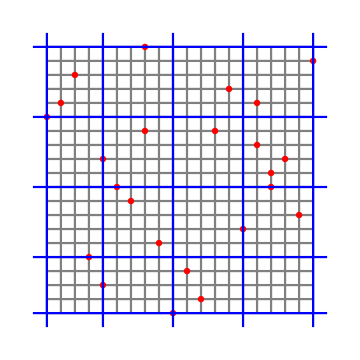

```mathematica
Show[Show[Table[p[z],{z,20}],Table[line[z],{z,20}],ListPlot[%94,PlotStyle->Red],(*ListPlot[{{3,12},{11,17},{20,8},{8,5}},PlotStyle->Black],*)PlotRange->All],Show[line1[1],line1[5],line1[10],line1[15],line1[20],PlotRange->All],Show[p1[1],p1[5],p1[10],p1[15],p1[20],PlotRange->All],Axes->False,ImageSize->{360,360},AspectRatio->Full]
```

```mathematica
Module[{},aa=Table[RandomSample[{imp13,imp1,imp18,imp16,imp17,imp10,imp11,imp14,imp12,imp8,imp15,imp19,imp2,imp9,imp7,imp5,imp6,imp3,imp20,imp4}],100];
bb:=Flatten[Table[Position[Flatten[Table[Position[aa[[1]],ToExpression[Table["imp"<>ToString[x]<>"",{x,20}][[y]]]],{y,20}]],z],{z,20}]];
leftright:= Transpose[Join[{Range[1,20,1]},{bb}]];
cc:=Flatten[Table[Position[bb,x],{x,Range[1,20,1]}]];
dd=ToExpression[Table["imp"<>ToString[z]<>"",{z,cc}]];
downup:=Transpose[Join[{cc},{Range[1,20,1]}]];{aa,dd}]
```

{{{imp3,imp2,imp14,imp9,imp19,imp17,imp12,imp8,imp15,imp13,imp16,imp18,imp4,imp6,imp5,imp7,imp20,imp1,imp11,imp10},{imp1,imp17,imp9,imp3,imp20,imp15,imp19,imp14,imp8,imp2,imp4,imp12,imp7,imp10,imp6,imp5,imp18,imp13,imp16,imp11},{imp18,imp14,imp19,imp3,imp7,imp11,imp4,imp20,imp17,imp9,imp1,imp2,imp16,imp13,imp5,imp12,imp15,imp10,imp8,imp6},{imp16,imp3,imp1,imp15,imp4,imp18,imp19,imp12,imp6,imp5,imp17,imp8,imp20,imp14,imp2,imp10,imp13,imp7,imp9,imp11},{imp6,imp11,imp13,imp5,imp19,imp15,imp18,imp4,imp12,imp7,imp3,imp8,imp2,imp1,imp20,imp9,imp10,imp16,imp17,imp14},{imp13,imp7,imp17,imp9,imp20,imp14,imp1,imp19,imp18,imp10,imp6,imp11,imp2,imp12,imp15,imp5,imp16,imp3,imp4,imp8},{imp6,imp12,imp20,imp2,imp7,imp3,imp1,imp17,imp4,imp8,imp16,imp13,imp14,imp5,imp18,imp10,imp15,imp11,imp9,imp19},{imp8,imp5,imp15,imp13,imp10,imp3,imp18,imp12,imp19,imp9,imp7,imp20,imp11,imp14,imp2,imp17,imp1,imp4,imp16,imp6},{imp8,imp1,imp7,imp2,imp15,imp20,imp10,imp6,imp11,imp5,imp4,imp18,imp3,imp16,imp13,imp17,imp14,imp19,imp9,imp12},{imp20,imp18,imp1,imp17,imp6,imp7,imp12,imp2,imp4,imp10,imp8,imp9,imp19,imp11,imp14,imp13,imp3,imp5,imp16,imp15},{imp17,imp19,imp9,imp8,imp12,imp3,imp13,imp5,imp11,imp14,imp16,imp20,imp1,imp15,imp2,imp4,imp18,imp10,imp7,imp6},{imp20,imp17,imp1,imp15,imp10,imp4,imp7,imp18,imp6,imp5,imp12,imp14,imp3,imp19,imp11,imp2,imp13,imp16,imp9,imp8},{imp8,imp9,imp13,imp1,imp17,imp11,imp19,imp18,imp20,imp14,imp2,imp10,imp5,imp16,imp12,imp7,imp4,imp15,imp6,imp3},{imp3,imp2,imp14,imp12,imp6,imp1,imp10,imp11,imp5,imp7,imp8,imp15,imp18,imp20,imp17,imp9,imp13,imp16,imp19,imp4},{imp11,imp13,imp1,imp17,imp12,imp20,imp6,imp2,imp10,imp5,imp19,imp9,imp14,imp18,imp3,imp4,imp15,imp8,imp16,imp7},{imp4,imp10,imp18,imp12,imp11,imp6,imp7,imp14,imp17,imp5,imp1,imp13,imp16,imp8,imp9,imp15,imp2,imp3,imp20,imp19},{imp12,imp3,imp15,imp5,imp16,imp10,imp18,imp14,imp17,imp11,imp7,imp9,imp1,imp20,imp2,imp8,imp4,imp6,imp13,imp19},{imp18,imp5,imp20,imp1,imp12,imp14,imp13,imp2,imp4,imp8,imp15,imp6,imp3,imp7,imp11,imp10,imp9,imp16,imp19,imp17},{imp9,imp19,imp8,imp16,imp17,imp12,imp14,imp15,imp10,imp6,imp5,imp11,imp4,imp13,imp7,imp3,imp1,imp18,imp2,imp20},{imp14,imp9,imp18,imp2,imp5,imp20,imp6,imp7,imp4,imp3,imp8,imp13,imp12,imp15,imp16,imp10,imp11,imp1,imp19,imp17},{imp19,imp14,imp20,imp11,imp16,imp2,imp4,imp17,imp13,imp9,imp15,imp1,imp18,imp7,imp12,imp10,imp6,imp8,imp3,imp5},{imp2,imp15,imp6,imp19,imp4,imp3,imp9,imp14,imp20,imp8,imp16,imp17,imp10,imp5,imp7,imp13,imp12,imp11,imp18,imp1},{imp3,imp16,imp11,imp9,imp14,imp17,imp7,imp1,imp8,imp6,imp20,imp15,imp18,imp4,imp12,imp13,imp19,imp2,imp10,imp5},{imp16,imp3,imp14,imp1,imp13,imp20,imp15,imp4,imp7,imp12,imp6,imp5,imp8,imp10,imp11,imp18,imp9,imp17,imp19,imp2},{imp20,imp9,imp8,imp14,imp6,imp2,imp4,imp3,imp19,imp10,imp13,imp18,imp16,imp11,imp12,imp7,imp15,imp5,imp17,imp1},{imp11,imp4,imp7,imp3,imp9,imp19,imp14,imp20,imp10,imp8,imp13,imp2,imp5,imp17,imp15,imp18,imp12,imp6,imp1,imp16},{imp17,imp10,imp6,imp16,imp13,imp15,imp4,imp18,imp8,imp11,imp5,imp3,imp12,imp19,imp9,imp20,imp7,imp14,imp1,imp2},{imp14,imp1,imp9,imp4,imp19,imp16,imp8,imp17,imp20,imp10,imp5,imp3,imp13,imp11,imp12,imp6,imp18,imp2,imp7,imp15},{imp17,imp7,imp15,imp10,imp2,imp20,imp11,imp5,imp18,imp6,imp14,imp3,imp16,imp13,imp8,imp4,imp1,imp12,imp9,imp19},{imp18,imp1,imp13,imp9,imp3,imp5,imp16,imp6,imp20,imp4,imp11,imp19,imp8,imp2,imp7,imp14,imp10,imp17,imp15,imp12},{imp4,imp17,imp6,imp18,imp11,imp14,imp12,imp10,imp20,imp3,imp19,imp16,imp1,imp15,imp7,imp2,imp5,imp8,imp13,imp9},{imp7,imp2,imp17,imp14,imp10,imp4,imp11,imp15,imp19,imp18,imp20,imp13,imp1,imp8,imp16,imp3,imp6,imp9,imp5,imp12},{imp17,imp14,imp13,imp9,imp3,imp18,imp5,imp6,imp2,imp7,imp1,imp8,imp11,imp20,imp16,imp15,imp19,imp10,imp4,imp12},{imp13,imp7,imp15,imp6,imp3,imp5,imp17,imp10,imp2,imp14,imp9,imp1,imp11,imp16,imp19,imp8,imp18,imp4,imp12,imp20},{imp6,imp1,imp2,imp13,imp18,imp20,imp9,imp19,imp16,imp17,imp7,imp14,imp5,imp3,imp10,imp12,imp11,imp4,imp8,imp15},{imp10,imp18,imp6,imp3,imp16,imp1,imp12,imp17,imp13,imp2,imp8,imp9,imp14,imp5,imp7,imp15,imp4,imp19,imp20,imp11},{imp12,imp4,imp13,imp16,imp8,imp1,imp17,imp6,imp19,imp20,imp7,imp10,imp2,imp14,imp9,imp11,imp5,imp18,imp3,imp15},{imp3,imp18,imp14,imp4,imp6,imp10,imp19,imp12,imp8,imp2,imp9,imp20,imp11,imp17,imp15,imp16,imp7,imp1,imp13,imp5},{imp1,imp15,imp20,imp3,imp14,imp18,imp9,imp8,imp5,imp2,imp10,imp6,imp11,imp16,imp13,imp19,imp12,imp17,imp4,imp7},{imp5,imp18,imp15,imp8,imp1,imp3,imp16,imp17,imp12,imp13,imp11,imp4,imp19,imp9,imp2,imp10,imp6,imp20,imp7,imp14},{imp3,imp16,imp6,imp7,imp14,imp17,imp15,imp12,imp1,imp5,imp9,imp20,imp4,imp2,imp13,imp8,imp10,imp19,imp18,imp11},{imp12,imp5,imp17,imp4,imp10,imp1,imp9,imp8,imp20,imp16,imp11,imp2,imp7,imp14,imp18,imp3,imp19,imp15,imp13,imp6},{imp18,imp5,imp10,imp4,imp16,imp19,imp9,imp11,imp14,imp7,imp3,imp15,imp2,imp12,imp20,imp13,imp17,imp1,imp8,imp6},{imp18,imp8,imp4,imp19,imp1,imp11,imp3,imp5,imp6,imp15,imp2,imp13,imp9,imp16,imp12,imp10,imp17,imp20,imp14,imp7},{imp14,imp5,imp8,imp9,imp7,imp6,imp16,imp10,imp11,imp17,imp13,imp2,imp20,imp19,imp18,imp3,imp4,imp1,imp15,imp12},{imp16,imp10,imp1,imp13,imp7,imp14,imp17,imp9,imp5,imp19,imp2,imp3,imp11,imp20,imp12,imp8,imp4,imp15,imp6,imp18},{imp12,imp6,imp11,imp18,imp8,imp1,imp4,imp20,imp9,imp19,imp15,imp14,imp3,imp7,imp13,imp5,imp2,imp17,imp10,imp16},{imp8,imp3,imp4,imp13,imp2,imp18,imp12,imp15,imp1,imp6,imp9,imp10,imp14,imp11,imp17,imp5,imp7,imp20,imp19,imp16},{imp8,imp6,imp16,imp18,imp11,imp1,imp9,imp4,imp10,imp12,imp5,imp20,imp14,imp19,imp2,imp17,imp13,imp3,imp15,imp7},{imp19,imp8,imp11,imp7,imp6,imp17,imp1,imp16,imp2,imp20,imp5,imp9,imp14,imp15,imp13,imp12,imp10,imp18,imp4,imp3},{imp17,imp1,imp7,imp19,imp15,imp10,imp12,imp20,imp5,imp8,imp6,imp14,imp11,imp3,imp16,imp18,imp4,imp13,imp2,imp9},{imp19,imp11,imp8,imp4,imp12,imp16,imp13,imp18,imp7,imp5,imp10,imp3,imp2,imp6,imp1,imp20,imp9,imp14,imp15,imp17},{imp13,imp11,imp16,imp8,imp10,imp12,imp2,imp1,imp18,imp19,imp17,imp14,imp9,imp4,imp6,imp7,imp20,imp5,imp3,imp15},{imp1,imp5,imp14,imp18,imp15,imp7,imp9,imp2,imp16,imp11,imp4,imp12,imp8,imp10,imp13,imp19,imp6,imp3,imp17,imp20},{imp10,imp6,imp11,imp19,imp14,imp5,imp3,imp13,imp12,imp9,imp7,imp1,imp2,imp15,imp8,imp4,imp18,imp20,imp17,imp16},{imp7,imp8,imp19,imp9,imp3,imp18,imp4,imp17,imp20,imp10,imp13,imp6,imp5,imp16,imp15,imp12,imp1,imp11,imp14,imp2},{imp18,imp9,imp19,imp4,imp8,imp7,imp1,imp11,imp20,imp16,imp6,imp3,imp14,imp12,imp5,imp2,imp17,imp13,imp15,imp10},{imp12,imp18,imp14,imp6,imp20,imp9,imp4,imp10,imp15,imp8,imp16,imp13,imp1,imp3,imp17,imp19,imp5,imp11,imp7,imp2},{imp19,imp17,imp8,imp20,imp18,imp9,imp2,imp6,imp16,imp11,imp1,imp13,imp5,imp15,imp14,imp7,imp4,imp3,imp12,imp10},{imp11,imp1,imp18,imp17,imp4,imp9,imp12,imp8,imp10,imp14,imp15,imp7,imp2,imp3,imp20,imp16,imp5,imp19,imp6,imp13},{imp2,imp17,imp20,imp1,imp3,imp15,imp10,imp7,imp6,imp12,imp19,imp8,imp9,imp13,imp5,imp4,imp16,imp18,imp14,imp11},{imp6,imp17,imp10,imp19,imp4,imp7,imp12,imp8,imp13,imp15,imp9,imp11,imp18,imp20,imp1,imp5,imp16,imp3,imp2,imp14},{imp5,imp19,imp1,imp14,imp8,imp12,imp20,imp3,imp2,imp13,imp7,imp16,imp4,imp18,imp10,imp15,imp6,imp17,imp9,imp11},{imp12,imp1,imp8,imp18,imp5,imp2,imp13,imp4,imp15,imp20,imp9,imp11,imp14,imp17,imp16,imp7,imp6,imp3,imp19,imp10},{imp16,imp15,imp17,imp1,imp12,imp9,imp6,imp18,imp2,imp13,imp11,imp20,imp10,imp19,imp5,imp8,imp7,imp3,imp14,imp4},{imp17,imp7,imp11,imp2,imp12,imp6,imp10,imp20,imp16,imp8,imp1,imp15,imp4,imp13,imp5,imp3,imp19,imp14,imp18,imp9},{imp13,imp11,imp7,imp8,imp16,imp17,imp4,imp14,imp20,imp2,imp12,imp5,imp18,imp19,imp6,imp9,imp10,imp15,imp1,imp3},{imp10,imp16,imp17,imp18,imp6,imp15,imp20,imp19,imp8,imp11,imp7,imp3,imp14,imp5,imp1,imp9,imp13,imp12,imp2,imp4},{imp5,imp3,imp4,imp9,imp15,imp18,imp16,imp6,imp2,imp17,imp14,imp11,imp8,imp7,imp20,imp19,imp13,imp1,imp12,imp10},{imp1,imp15,imp8,imp19,imp7,imp2,imp4,imp10,imp9,imp17,imp12,imp20,imp16,imp14,imp18,imp13,imp6,imp5,imp3,imp11},{imp1,imp7,imp3,imp4,imp8,imp16,imp19,imp5,imp18,imp10,imp14,imp20,imp9,imp17,imp2,imp11,imp12,imp13,imp6,imp15},{imp3,imp14,imp2,imp19,imp17,imp8,imp10,imp6,imp16,imp20,imp11,imp7,imp18,imp15,imp1,imp4,imp9,imp12,imp13,imp5},{imp16,imp12,imp8,imp4,imp18,imp2,imp6,imp14,imp10,imp7,imp17,imp11,imp3,imp15,imp20,imp9,imp13,imp1,imp5,imp19},{imp4,imp20,imp11,imp13,imp2,imp3,imp14,imp6,imp8,imp9,imp17,imp1,imp16,imp15,imp5,imp18,imp10,imp12,imp7,imp19},{imp13,imp15,imp9,imp7,imp3,imp12,imp8,imp18,imp5,imp20,imp6,imp17,imp2,imp14,imp4,imp1,imp10,imp16,imp11,imp19},{imp1,imp16,imp15,imp2,imp18,imp4,imp14,imp10,imp3,imp20,imp7,imp5,imp9,imp19,imp17,imp13,imp8,imp11,imp6,imp12},{imp2,imp16,imp6,imp19,imp20,imp4,imp5,imp1,imp10,imp12,imp17,imp7,imp11,imp15,imp14,imp3,imp18,imp13,imp9,imp8},{imp8,imp20,imp9,imp7,imp11,imp12,imp3,imp17,imp10,imp5,imp1,imp19,imp2,imp6,imp15,imp16,imp18,imp4,imp13,imp14},{imp4,imp8,imp12,imp20,imp10,imp18,imp13,imp14,imp9,imp15,imp3,imp7,imp17,imp16,imp6,imp2,imp1,imp5,imp11,imp19},{imp18,imp4,imp5,imp9,imp20,imp10,imp19,imp8,imp2,imp3,imp12,imp13,imp14,imp7,imp6,imp11,imp15,imp1,imp17,imp16},{imp20,imp5,imp11,imp10,imp4,imp1,imp6,imp16,imp18,imp19,imp14,imp12,imp8,imp9,imp15,imp2,imp3,imp13,imp7,imp17},{imp8,imp19,imp17,imp6,imp4,imp15,imp11,imp10,imp2,imp12,imp13,imp3,imp14,imp1,imp18,imp16,imp9,imp20,imp7,imp5},{imp18,imp15,imp10,imp14,imp9,imp6,imp11,imp19,imp1,imp3,imp12,imp17,imp16,imp2,imp4,imp5,imp13,imp20,imp8,imp7},{imp20,imp8,imp6,imp12,imp2,imp3,imp11,imp14,imp17,imp18,imp9,imp15,imp4,imp13,imp19,imp10,imp7,imp1,imp16,imp5},{imp15,imp12,imp4,imp13,imp7,imp6,imp10,imp18,imp16,imp1,imp17,imp8,imp11,imp2,imp20,imp14,imp3,imp9,imp19,imp5},{imp6,imp7,imp16,imp20,imp8,imp10,imp12,imp4,imp5,imp9,imp3,imp11,imp13,imp17,imp14,imp19,imp15,imp18,imp1,imp2},{imp5,imp15,imp19,imp12,imp1,imp13,imp11,imp6,imp14,imp16,imp2,imp10,imp18,imp9,imp3,imp4,imp7,imp17,imp20,imp8},{imp5,imp10,imp9,imp19,imp4,imp8,imp7,imp16,imp20,imp11,imp18,imp3,imp13,imp15,imp2,imp17,imp12,imp14,imp6,imp1},{imp9,imp20,imp15,imp1,imp18,imp4,imp16,imp6,imp2,imp8,imp10,imp3,imp12,imp17,imp13,imp5,imp7,imp11,imp19,imp14},{imp2,imp5,imp19,imp9,imp6,imp12,imp17,imp8,imp11,imp4,imp14,imp13,imp7,imp3,imp20,imp18,imp10,imp1,imp15,imp16},{imp1,imp9,imp15,imp8,imp18,imp16,imp5,imp17,imp11,imp10,imp19,imp6,imp7,imp14,imp12,imp4,imp3,imp2,imp20,imp13},{imp17,imp9,imp10,imp19,imp15,imp16,imp14,imp7,imp1,imp3,imp11,imp8,imp4,imp2,imp18,imp13,imp5,imp6,imp12,imp20},{imp11,imp20,imp8,imp17,imp10,imp2,imp16,imp1,imp7,imp5,imp15,imp19,imp12,imp6,imp3,imp18,imp4,imp13,imp14,imp9},{imp15,imp16,imp4,imp12,imp20,imp14,imp18,imp19,imp17,imp5,imp10,imp7,imp6,imp13,imp2,imp9,imp8,imp3,imp11,imp1},{imp5,imp2,imp17,imp16,imp18,imp10,imp14,imp13,imp9,imp7,imp12,imp6,imp4,imp1,imp15,imp19,imp11,imp8,imp20,imp3},{imp9,imp19,imp7,imp12,imp18,imp2,imp17,imp20,imp4,imp14,imp16,imp8,imp13,imp3,imp10,imp1,imp11,imp5,imp6,imp15},{imp4,imp7,imp2,imp8,imp12,imp10,imp19,imp5,imp17,imp18,imp15,imp9,imp16,imp13,imp3,imp20,imp11,imp6,imp1,imp14},{imp11,imp15,imp10,imp20,imp3,imp12,imp13,imp17,imp19,imp9,imp5,imp4,imp7,imp6,imp16,imp18,imp8,imp14,imp2,imp1},{imp9,imp19,imp13,imp5,imp7,imp11,imp17,imp6,imp18,imp12,imp3,imp4,imp10,imp2,imp1,imp15,imp14,imp16,imp20,imp8},{imp5,imp13,imp2,imp14,imp9,imp3,imp18,imp8,imp19,imp12,imp11,imp1,imp6,imp16,imp10,imp7,imp15,imp17,imp20,imp4}},{imp18,imp2,imp1,imp13,imp15,imp14,imp16,imp8,imp4,imp20,imp19,imp7,imp10,imp3,imp9,imp11,imp6,imp12,imp5,imp17}}

```mathematica
bb
```

{11,14,2,9,6,8,15,4,1,13,18,3,12,5,17,10,7,19,20,16}

```mathematica
Table[Extract[bb,x],{x,Range[1,12,1]}]
```

{11,14,2,9,6,8,15,4,1,13,18,3}

```mathematica
Length[%159]
```

12

```mathematica
Position[aa,imp2]
Position[aa,imp6]
Position[aa,imp13]
Position[aa,imp18]
```

```mathematica
Position[dd,imp2]
Position[dd,imp6]
Position[dd,imp13]
Position[dd,imp18]
```

```mathematica
Clear[imp13,imp1,imp18,imp16,imp17,imp10,imp11,imp14,imp12,imp8,imp15,imp19,imp2,imp9,imp7,imp5,imp6,imp3,imp20,imp4,aa,bb,cc]
```

```mathematica
aa=Table[RandomSample[{imp13,imp1,imp18,imp16,imp17,imp10,imp11,imp14,imp12,imp8,imp15,imp19,imp2,imp9,imp7,imp5,imp6,imp3,imp20,imp4}],100]
bb=Table[Flatten[Table[Position[Flatten[Table[Position[aa[[n]],ToExpression[Table["imp"<>ToString[x]<>"",{x,20}][[y]]]],{y,20}]],z],{z,20}]],{n,100}]
cc=Table[Flatten[Table[Position[bb[[n]],x],{x,Range[1,20,1]}]],{n,100}]
dd=Table[ToExpression[Table["imp"<>ToString[z]<>"",{z,cc[[xx]]}]],{xx,100}]
```

{{imp16,imp19,imp4,imp18,imp8,imp12,imp20,imp6,imp9,imp3,imp15,imp10,imp14,imp17,imp1,imp2,imp13,imp7,imp5,imp11},{imp16,imp2,imp14,imp7,imp18,imp20,imp12,imp3,imp13,imp1,imp15,imp10,imp11,imp8,imp4,imp17,imp19,imp9,imp5,imp6},{imp14,imp16,imp20,imp12,imp1,imp11,imp5,imp10,imp2,imp15,imp9,imp13,imp7,imp19,imp18,imp3,imp17,imp4,imp6,imp8},{imp2,imp19,imp16,imp4,imp10,imp9,imp14,imp18,imp5,imp7,imp17,imp11,imp12,imp1,imp3,imp13,imp20,imp6,imp8,imp15},{imp19,imp11,imp10,imp12,imp9,imp8,imp17,imp15,imp1,imp18,imp5,imp2,imp7,imp3,imp16,imp14,imp4,imp20,imp13,imp6},{imp18,imp19,imp12,imp8,imp5,imp13,imp6,imp20,imp10,imp14,imp4,imp17,imp15,imp16,imp3,imp2,imp1,imp7,imp11,imp9},{imp9,imp11,imp3,imp7,imp16,imp15,imp1,imp4,imp18,imp17,imp13,imp2,imp6,imp10,imp20,imp14,imp12,imp19,imp8,imp5},{imp6,imp15,imp17,imp20,imp11,imp9,imp5,imp16,imp8,imp14,imp18,imp7,imp10,imp19,imp2,imp1,imp12,imp3,imp4,imp13},{imp1,imp7,imp17,imp19,imp5,imp18,imp20,imp12,imp3,imp11,imp14,imp9,imp8,imp10,imp4,imp15,imp16,imp6,imp13,imp2},{imp11,imp19,imp4,imp18,imp9,imp2,imp8,imp20,imp3,imp16,imp7,imp6,imp14,imp17,imp13,imp12,imp15,imp1,imp5,imp10},{imp15,imp20,imp3,imp13,imp12,imp1,imp7,imp4,imp8,imp19,imp16,imp5,imp10,imp6,imp18,imp2,imp11,imp9,imp14,imp17},{imp4,imp11,imp10,imp15,imp13,imp7,imp18,imp5,imp16,imp19,imp17,imp3,imp14,imp1,imp2,imp20,imp8,imp9,imp6,imp12},{imp6,imp3,imp9,imp10,imp18,imp1,imp2,imp12,imp19,imp20,imp4,imp16,imp13,imp15,imp11,imp8,imp14,imp17,imp7,imp5},{imp13,imp19,imp7,imp12,imp4,imp17,imp15,imp2,imp8,imp14,imp10,imp3,imp5,imp16,imp11,imp6,imp1,imp18,imp20,imp9},{imp14,imp5,imp1,imp12,imp8,imp7,imp16,imp10,imp9,imp17,imp19,imp4,imp2,imp11,imp13,imp3,imp6,imp18,imp15,imp20},{imp18,imp4,imp16,imp20,imp13,imp12,imp15,imp10,imp9,imp1,imp17,imp8,imp14,imp7,imp3,imp2,imp5,imp19,imp6,imp11},{imp9,imp14,imp12,imp19,imp11,imp13,imp1,imp18,imp6,imp5,imp7,imp15,imp16,imp8,imp10,imp20,imp2,imp17,imp3,imp4},{imp15,imp10,imp2,imp8,imp19,imp12,imp11,imp3,imp20,imp5,imp7,imp14,imp6,imp16,imp13,imp4,imp17,imp9,imp1,imp18},{imp17,imp20,imp7,imp1,imp3,imp14,imp13,imp8,imp19,imp2,imp16,imp15,imp18,imp12,imp6,imp10,imp11,imp9,imp5,imp4},{imp7,imp4,imp2,imp15,imp9,imp3,imp6,imp10,imp19,imp20,imp12,imp5,imp11,imp18,imp14,imp17,imp1,imp8,imp13,imp16},{imp2,imp14,imp11,imp7,imp20,imp5,imp15,imp8,imp4,imp6,imp12,imp16,imp10,imp9,imp1,imp18,imp13,imp19,imp3,imp17},{imp5,imp4,imp10,imp16,imp20,imp7,imp3,imp13,imp9,imp2,imp14,imp1,imp12,imp6,imp19,imp15,imp17,imp11,imp18,imp8},{imp7,imp15,imp12,imp6,imp2,imp11,imp19,imp17,imp4,imp20,imp14,imp18,imp16,imp8,imp3,imp13,imp5,imp10,imp1,imp9},{imp15,imp1,imp6,imp19,imp7,imp10,imp8,imp20,imp18,imp2,imp9,imp3,imp16,imp5,imp14,imp4,imp11,imp17,imp12,imp13},{imp11,imp12,imp3,imp7,imp17,imp1,imp18,imp2,imp9,imp8,imp13,imp10,imp4,imp20,imp6,imp16,imp5,imp15,imp19,imp14},{imp5,imp4,imp20,imp12,imp8,imp17,imp14,imp1,imp2,imp16,imp18,imp9,imp7,imp3,imp13,imp10,imp19,imp15,imp6,imp11},{imp1,imp7,imp16,imp10,imp13,imp19,imp20,imp6,imp3,imp9,imp8,imp18,imp2,imp15,imp4,imp12,imp5,imp14,imp17,imp11},{imp15,imp18,imp2,imp16,imp13,imp12,imp8,imp1,imp4,imp17,imp6,imp9,imp5,imp19,imp11,imp20,imp7,imp3,imp10,imp14},{imp1,imp7,imp2,imp19,imp10,imp16,imp18,imp17,imp15,imp9,imp13,imp12,imp14,imp4,imp5,imp20,imp8,imp11,imp3,imp6},{imp3,imp18,imp11,imp4,imp15,imp8,imp16,imp17,imp14,imp9,imp19,imp10,imp20,imp1,imp13,imp7,imp2,imp6,imp5,imp12},{imp18,imp4,imp10,imp7,imp12,imp13,imp3,imp19,imp11,imp1,imp17,imp15,imp2,imp5,imp14,imp16,imp9,imp20,imp8,imp6},{imp20,imp15,imp12,imp5,imp8,imp4,imp17,imp13,imp16,imp14,imp19,imp6,imp3,imp10,imp9,imp2,imp18,imp1,imp11,imp7},{imp4,imp7,imp20,imp8,imp6,imp1,imp2,imp18,imp5,imp12,imp3,imp13,imp17,imp10,imp16,imp14,imp15,imp11,imp9,imp19},{imp7,imp20,imp8,imp5,imp3,imp13,imp16,imp19,imp11,imp10,imp12,imp14,imp2,imp17,imp1,imp18,imp4,imp15,imp6,imp9},{imp20,imp10,imp3,imp14,imp12,imp5,imp19,imp15,imp7,imp17,imp1,imp11,imp13,imp6,imp8,imp16,imp18,imp9,imp4,imp2},{imp2,imp10,imp12,imp14,imp20,imp11,imp7,imp6,imp18,imp3,imp16,imp1,imp13,imp4,imp15,imp17,imp19,imp8,imp5,imp9},{imp19,imp17,imp10,imp14,imp7,imp2,imp9,imp16,imp8,imp6,imp15,imp13,imp3,imp11,imp5,imp20,imp18,imp4,imp1,imp12},{imp16,imp8,imp2,imp18,imp11,imp19,imp20,imp3,imp6,imp4,imp9,imp5,imp10,imp15,imp17,imp7,imp12,imp13,imp14,imp1},{imp11,imp5,imp15,imp13,imp3,imp8,imp12,imp1,imp6,imp16,imp4,imp20,imp17,imp10,imp19,imp9,imp7,imp14,imp18,imp2},{imp16,imp12,imp9,imp11,imp2,imp3,imp14,imp8,imp20,imp10,imp18,imp13,imp5,imp4,imp1,imp17,imp19,imp6,imp7,imp15},{imp16,imp12,imp5,imp11,imp4,imp17,imp14,imp9,imp2,imp19,imp8,imp10,imp20,imp3,imp15,imp13,imp7,imp18,imp1,imp6},{imp1,imp15,imp8,imp6,imp9,imp19,imp10,imp4,imp16,imp2,imp7,imp5,imp14,imp11,imp17,imp20,imp18,imp3,imp12,imp13},{imp13,imp7,imp12,imp17,imp8,imp3,imp11,imp19,imp1,imp18,imp5,imp4,imp2,imp16,imp9,imp6,imp14,imp20,imp10,imp15},{imp14,imp7,imp15,imp4,imp9,imp6,imp17,imp16,imp8,imp19,imp5,imp20,imp2,imp12,imp11,imp3,imp1,imp13,imp10,imp18},{imp11,imp12,imp16,imp2,imp6,imp1,imp17,imp20,imp8,imp3,imp19,imp4,imp5,imp15,imp14,imp13,imp7,imp18,imp9,imp10},{imp16,imp13,imp20,imp4,imp6,imp8,imp2,imp18,imp1,imp3,imp17,imp15,imp9,imp11,imp10,imp7,imp14,imp19,imp12,imp5},{imp16,imp15,imp11,imp1,imp12,imp9,imp3,imp8,imp5,imp13,imp14,imp10,imp19,imp18,imp7,imp17,imp2,imp20,imp4,imp6},{imp17,imp3,imp15,imp8,imp1,imp11,imp13,imp4,imp7,imp10,imp2,imp19,imp6,imp18,imp14,imp9,imp16,imp20,imp5,imp12},{imp13,imp15,imp12,imp7,imp10,imp3,imp17,imp1,imp16,imp2,imp19,imp5,imp8,imp4,imp9,imp18,imp14,imp20,imp6,imp11},{imp9,imp2,imp3,imp18,imp13,imp20,imp12,imp1,imp11,imp4,imp14,imp19,imp8,imp5,imp16,imp15,imp17,imp10,imp6,imp7},{imp17,imp4,imp15,imp18,imp3,imp5,imp10,imp16,imp9,imp2,imp12,imp20,imp11,imp8,imp6,imp13,imp19,imp7,imp14,imp1},{imp10,imp12,imp13,imp7,imp18,imp19,imp6,imp5,imp8,imp4,imp9,imp16,imp14,imp11,imp3,imp15,imp2,imp20,imp1,imp17},{imp4,imp18,imp9,imp14,imp10,imp13,imp1,imp19,imp12,imp3,imp16,imp20,imp8,imp17,imp15,imp2,imp5,imp6,imp7,imp11},{imp11,imp12,imp13,imp19,imp3,imp5,imp14,imp6,imp20,imp10,imp16,imp4,imp7,imp15,imp18,imp17,imp9,imp1,imp8,imp2},{imp3,imp15,imp18,imp19,imp14,imp5,imp16,imp2,imp9,imp8,imp20,imp7,imp17,imp10,imp6,imp1,imp13,imp4,imp12,imp11},{imp19,imp14,imp18,imp1,imp16,imp11,imp17,imp6,imp3,imp12,imp7,imp15,imp4,imp5,imp9,imp20,imp2,imp10,imp13,imp8},{imp20,imp14,imp9,imp19,imp3,imp7,imp6,imp16,imp15,imp8,imp2,imp11,imp17,imp10,imp12,imp18,imp5,imp4,imp13,imp1},{imp5,imp17,imp6,imp3,imp7,imp19,imp1,imp18,imp11,imp9,imp16,imp10,imp14,imp2,imp15,imp12,imp13,imp20,imp8,imp4},{imp18,imp6,imp8,imp15,imp5,imp17,imp16,imp20,imp3,imp9,imp4,imp12,imp7,imp10,imp1,imp2,imp13,imp11,imp14,imp19},{imp17,imp5,imp7,imp16,imp1,imp14,imp6,imp18,imp11,imp8,imp13,imp4,imp10,imp20,imp15,imp3,imp2,imp9,imp12,imp19},{imp3,imp15,imp13,imp10,imp5,imp7,imp6,imp19,imp20,imp4,imp18,imp9,imp2,imp12,imp17,imp11,imp1,imp14,imp16,imp8},{imp7,imp11,imp14,imp5,imp2,imp12,imp3,imp8,imp18,imp1,imp15,imp17,imp20,imp13,imp9,imp6,imp10,imp16,imp4,imp19},{imp16,imp9,imp19,imp11,imp6,imp5,imp12,imp13,imp2,imp1,imp4,imp14,imp18,imp3,imp7,imp15,imp17,imp20,imp8,imp10},{imp15,imp6,imp13,imp4,imp20,imp10,imp9,imp5,imp17,imp8,imp12,imp18,imp19,imp14,imp7,imp2,imp3,imp16,imp1,imp11},{imp4,imp10,imp16,imp18,imp1,imp19,imp12,imp14,imp2,imp5,imp15,imp17,imp11,imp13,imp3,imp9,imp8,imp6,imp7,imp20},{imp14,imp16,imp11,imp17,imp15,imp12,imp4,imp1,imp3,imp19,imp7,imp8,imp5,imp18,imp20,imp6,imp2,imp10,imp9,imp13},{imp8,imp13,imp4,imp17,imp9,imp6,imp14,imp2,imp5,imp19,imp20,imp11,imp15,imp18,imp7,imp12,imp1,imp10,imp16,imp3},{imp11,imp7,imp17,imp15,imp2,imp19,imp12,imp14,imp1,imp10,imp13,imp8,imp20,imp6,imp16,imp9,imp3,imp18,imp4,imp5},{imp5,imp6,imp10,imp20,imp17,imp1,imp16,imp9,imp15,imp13,imp8,imp18,imp2,imp12,imp4,imp11,imp7,imp19,imp3,imp14},{imp17,imp3,imp4,imp18,imp7,imp10,imp19,imp6,imp13,imp9,imp8,imp12,imp1,imp15,imp20,imp2,imp16,imp14,imp5,imp11},{imp14,imp5,imp7,imp6,imp1,imp4,imp3,imp10,imp8,imp11,imp20,imp16,imp17,imp19,imp13,imp18,imp12,imp15,imp2,imp9},{imp17,imp4,imp16,imp18,imp10,imp20,imp5,imp1,imp9,imp2,imp19,imp8,imp14,imp12,imp13,imp7,imp3,imp11,imp15,imp6},{imp13,imp6,imp19,imp5,imp7,imp16,imp17,imp4,imp10,imp18,imp11,imp9,imp3,imp12,imp1,imp20,imp8,imp14,imp15,imp2},{imp10,imp14,imp18,imp17,imp12,imp8,imp9,imp7,imp2,imp4,imp6,imp16,imp11,imp15,imp5,imp3,imp13,imp19,imp1,imp20},{imp1,imp12,imp4,imp19,imp3,imp8,imp7,imp11,imp13,imp5,imp17,imp18,imp10,imp2,imp14,imp9,imp6,imp16,imp20,imp15},{imp17,imp13,imp9,imp5,imp18,imp8,imp20,imp15,imp4,imp7,imp12,imp19,imp10,imp3,imp14,imp6,imp2,imp1,imp11,imp16},{imp9,imp3,imp19,imp4,imp2,imp13,imp12,imp8,imp7,imp14,imp1,imp15,imp18,imp17,imp10,imp11,imp5,imp16,imp6,imp20},{imp5,imp6,imp10,imp11,imp18,imp17,imp9,imp19,imp20,imp4,imp2,imp7,imp8,imp12,imp1,imp16,imp14,imp13,imp15,imp3},{imp15,imp10,imp16,imp12,imp3,imp11,imp5,imp17,imp4,imp18,imp13,imp2,imp9,imp6,imp1,imp8,imp20,imp19,imp7,imp14},{imp16,imp7,imp11,imp18,imp10,imp8,imp20,imp9,imp6,imp12,imp14,imp19,imp4,imp15,imp1,imp13,imp3,imp17,imp5,imp2},{imp17,imp3,imp10,imp15,imp11,imp8,imp18,imp2,imp1,imp7,imp5,imp20,imp9,imp12,imp16,imp14,imp13,imp4,imp6,imp19},{imp10,imp16,imp19,imp1,imp14,imp3,imp4,imp18,imp12,imp9,imp6,imp15,imp7,imp11,imp17,imp13,imp20,imp8,imp5,imp2},{imp19,imp14,imp4,imp1,imp10,imp15,imp9,imp3,imp12,imp5,imp16,imp8,imp2,imp11,imp17,imp18,imp20,imp6,imp7,imp13},{imp5,imp10,imp4,imp6,imp8,imp18,imp2,imp20,imp14,imp19,imp12,imp17,imp9,imp15,imp7,imp11,imp13,imp1,imp3,imp16},{imp18,imp5,imp6,imp11,imp10,imp8,imp9,imp14,imp17,imp13,imp19,imp16,imp15,imp7,imp2,imp12,imp1,imp20,imp4,imp3},{imp10,imp8,imp16,imp20,imp15,imp1,imp2,imp17,imp14,imp13,imp6,imp7,imp4,imp18,imp3,imp19,imp5,imp9,imp11,imp12},{imp12,imp3,imp6,imp11,imp1,imp2,imp14,imp7,imp16,imp17,imp4,imp20,imp15,imp10,imp8,imp9,imp18,imp13,imp5,imp19},{imp17,imp7,imp1,imp15,imp13,imp11,imp9,imp3,imp18,imp19,imp8,imp20,imp16,imp6,imp4,imp12,imp5,imp14,imp10,imp2},{imp15,imp7,imp18,imp17,imp14,imp10,imp9,imp20,imp13,imp1,imp16,imp2,imp19,imp6,imp8,imp4,imp5,imp12,imp3,imp11},{imp11,imp12,imp1,imp20,imp9,imp3,imp15,imp2,imp5,imp4,imp16,imp19,imp8,imp10,imp7,imp17,imp13,imp14,imp6,imp18},{imp17,imp20,imp19,imp15,imp12,imp6,imp16,imp9,imp4,imp7,imp11,imp18,imp10,imp5,imp8,imp2,imp14,imp3,imp13,imp1},{imp3,imp8,imp11,imp10,imp12,imp18,imp4,imp14,imp13,imp2,imp19,imp16,imp6,imp17,imp5,imp15,imp9,imp1,imp20,imp7},{imp19,imp7,imp6,imp12,imp20,imp1,imp15,imp2,imp13,imp5,imp14,imp11,imp17,imp16,imp10,imp8,imp9,imp18,imp3,imp4},{imp12,imp8,imp20,imp19,imp16,imp15,imp13,imp1,imp2,imp18,imp4,imp6,imp7,imp5,imp9,imp10,imp11,imp17,imp3,imp14},{imp11,imp4,imp9,imp5,imp17,imp14,imp3,imp19,imp12,imp8,imp6,imp1,imp13,imp20,imp7,imp15,imp16,imp2,imp18,imp10},{imp16,imp2,imp17,imp4,imp20,imp3,imp19,imp14,imp18,imp1,imp11,imp13,imp10,imp15,imp8,imp6,imp9,imp7,imp5,imp12},{imp14,imp11,imp13,imp3,imp19,imp16,imp4,imp5,imp8,imp9,imp6,imp1,imp12,imp15,imp18,imp10,imp2,imp7,imp20,imp17},{imp4,imp17,imp15,imp6,imp1,imp3,imp5,imp16,imp9,imp7,imp13,imp10,imp20,imp11,imp8,imp2,imp18,imp12,imp14,imp19},{imp3,imp10,imp20,imp16,imp8,imp15,imp12,imp14,imp1,imp9,imp11,imp4,imp17,imp7,imp19,imp2,imp6,imp5,imp13,imp18},{imp6,imp17,imp16,imp15,imp13,imp4,imp2,imp8,imp11,imp19,imp3,imp5,imp12,imp7,imp10,imp9,imp14,imp1,imp20,imp18}}